## Parameters

```mathematica
m = 0.973; (*Kg*)
g = 9.81;
Iz =0.0016155926; (*Kg m^2*) 
W = 1.3780;
w = 0.1694;
l = 1;
```

## Kinematics

```mathematica
KineChainEQ[1] =l(Cos[ϕ1[t]]+Cos[ϕ2[t]])+w*Cos[α[t]]-W==0;
KineChainEQ[2] = l(-Sin[ϕ1[t]]+Sin[ϕ2[t]])+w*Sin[α[t]]==0;
KineChainEQList = KineChainEQ/@{1,2}
```

{-1.378+0.1694 Cos[α[t]]+Cos[ϕ1[t]]+Cos[ϕ2[t]]==0,0.1694 Sin[α[t]]-Sin[ϕ1[t]]+Sin[ϕ2[t]]==0}

```mathematica
KineConstraints = {l1>0, l2>0, -π/2<α<π/2, 0<ϕ1<π/2, 0<ϕ2<π/2};
```

```mathematica
KineChainEQReduced = Assuming[KineConstraints, Eliminate[KineChainEQList, ϕ2[t]]]//Simplify
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

5.68943+Cos[α[t]] (-1.378+1. Cos[ϕ1[t]])==8.13459 Cos[ϕ1[t]]+1. Sin[α[t]] Sin[ϕ1[t]]

```mathematica
FConstraint = KineChainEQReduced[[1]]-KineChainEQReduced[[2]]
```

5.68943-8.13459 Cos[ϕ1[t]]+Cos[α[t]] (-1.378+1. Cos[ϕ1[t]])-1. Sin[α[t]] Sin[ϕ1[t]]

## Kinetic Energy (T)

```mathematica
r = l*{Cos[ϕ1[t]], -Sin[ϕ1[t]]}+w/2*{Cos[α[t]], Sin[α[t]]};
v = Sqrt[D[r[[1]],t]^2+D[r[[2]],t]^2];
ω = D[α[t],t];
T= 1/2 m v^2 +1/2 Iz ω^2
```

0.000807796 α'[t]^2+0.4865 ((0.0847 Cos[α[t]] α'[t]-Cos[ϕ1[t]] ϕ1'[t])^2+(-0.0847 Sin[α[t]] α'[t]-Sin[ϕ1[t]] ϕ1'[t])^2)

## Potential Energy (U)

```mathematica
U= m*g*r[[2]]
```

9.54513 (0.0847 Sin[α[t]]-Sin[ϕ1[t]])

## Lagrange Equations

```mathematica
L= T-U
```

-9.54513 (0.0847 Sin[α[t]]-Sin[ϕ1[t]])+0.000807796 α'[t]^2+0.4865 ((0.0847 Cos[α[t]] α'[t]-Cos[ϕ1[t]] ϕ1'[t])^2+(-0.0847 Sin[α[t]] α'[t]-Sin[ϕ1[t]] ϕ1'[t])^2)

Lagrange Equations for x,y,α:

```mathematica
LEQ[q_] := D[D[L,q'[t]],t]-D[L,q[t]]-λ[t]*D[FConstraint, q[t]]==0
```

```mathematica
allLEQ = LEQ/@{ϕ1,α}//Simplify
```

{1. Cos[ϕ1[t]]+(0.852224 Sin[ϕ1[t]]-0.104765 Sin[α[t]+ϕ1[t]]) λ[t]+0.00863405 Cos[α[t]+ϕ1[t]] α''[t]==0.00863405 Sin[α[t]+ϕ1[t]] α'[t]^2+0.101937 ϕ1''[t],1. Cos[α[t]]+(-1.70445 Sin[α[t]]+1.2369 Sin[α[t]+ϕ1[t]]) λ[t]+0.101937 Sin[α[t]+ϕ1[t]] ϕ1'[t]^2+0.0106324 α''[t]==0.101937 Cos[α[t]+ϕ1[t]] ϕ1''[t]}

## Combine and Integrate

```mathematica
Solve[FConstraint==0/.α[t]->1Degree,ϕ1[t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ1[t]→-0.919445},{ϕ1[t]→0.924337}}

```mathematica
initC = {α[0]==20 Degree, α'[0] == 0, ϕ1[0]==0.9243369639138412, ϕ1'[0]==0};
sol = NDSolve[Join[{FConstraint==0},allLEQ, initC],{α,ϕ1,λ},{t,0,1}, Method->{"IndexReduction"->Automatic}]
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{{α→InterpolatingFunction[…],ϕ1→InterpolatingFunction[…],λ→InterpolatingFunction[…]}}

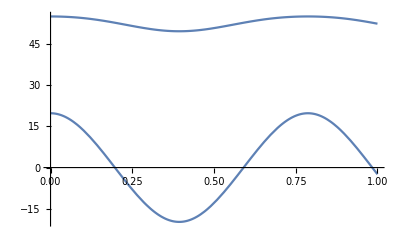

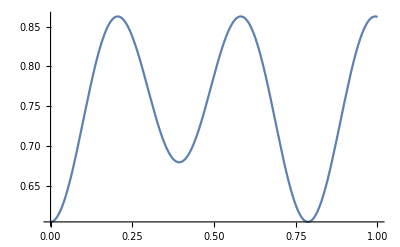

```mathematica
Plot[180/π*{α[t], ϕ1[t]}/.First@sol,{t,0, 1}]
Plot[λ[t]*D[FConstraint, α[t]]/.First@sol,{t,0,1}]
```